# Clock uncertainty relation Code and data used to generate plots in Prech et al., Optimal time estimation and the clock uncertainty relation for stochastic processes

## Basic definitions

```mathematica
(*Construct a random ring graph and its rate matrix*)
randomRing[gammas_]:=Module[{d,gamL,gamR,L},
(*Define rate matrix*)
d = Length[gammas[[1]]];
gamR=gammas[[1,;;]];gamL=gammas[[2,;;]];
L =DiagonalMatrix[gamL[[;;-2]],1]+DiagonalMatrix[gamR[[;;-2]],-1];
L[[d,1]]=gamL[[d]];L[[1,d]]=gamR[[d]];
L-DiagonalMatrix[Total[L]]
]
(* Random graph rate matrix *)
randomSparseGraph[f_,d_]:=Module[{A,G,L,connected=False},
While[connected==False,
(* Define adjacency matrix *)
A = RandomChoice[{1-f,f}->{0,1},{d,d}];
(* Check the corresponding graph is connected *)
G=AdjacencyGraph[A];
connected=ConnectedGraphQ[G];
];
(*Define rate matrix*)
L=RandomReal[1,{d,d}];
L = A*L;
L-DiagonalMatrix[Total[L]]
]
(* Find the steady state *)
steadyState[L_]:=Module[{eigs,p,ind},
eigs=Eigensystem[L];
ind=Position[Chop[eigs[[1]]],0][[1,1]];
p=eigs[[2,ind]];
p/Total[p]//Re
]
(* Find average current given weights w *) 
meanCurrent[L_,p_,w_]:=Module[{R,d},
d=Length[p];
R=L-DiagonalMatrix[Diagonal[L]];
Sum[R[[i,j]]p[[j]]w[[i,j]],{i,d},{j,d}]
]
(* Find the diffusion coefficient given weights w  *) 
diffusionCoeff[L_,p_,w_]:=Module[{Ld,R,d,𝒟},
d=Length[p];
Ld=DrazinInverse[L];
R=L-DiagonalMatrix[Diagonal[L]];
𝒟[i_,j_,k_,l_]:=KroneckerDelta[i,k]KroneckerDelta[j,l]R[[k,l]]p[[l]]-R[[i,j]]Ld[[j,k]]R[[k,l]]p[[l]]-R[[k,l]]Ld[[l,i]]R[[i,j]]p[[j]];
Sum[w[[i,j]]𝒟[i,j,k,l]w[[k,l]],{i,d},{j,d},{k,d},{l,d}]
]
(* Find the dynamical activity 𝒜, mean waiting time 𝒯 and entropy production rate 𝒮 *)
activities[L_,p_]:=Module[{d,R,Γ,𝒜,𝒯,𝒮,s},
d=Length[p];
Γ=-Diagonal[L];
R=L-DiagonalMatrix[Diagonal[L]];
𝒜=Γ.p;
𝒯=(1/Γ).p;
𝒮=Sum[If[R[[i,j]]!=0,Log[R[[i,j]]/R[[j,i]]]R[[i,j]]p[[j]],0],{i,d},{j,d}];
{𝒜,𝒯,𝒮}
]
```

## Trajectories (Fig. 2)

```mathematica
(* Find the time and type of the next jump *)
sampleJump[L_,σ_]:=Module[{t,μ,r,Γ,R},
r=RandomReal[];
Γ=-L[[σ,σ]];
t=-Log[r]/Γ;
r=RandomReal[];
R=L[[;;,σ]];
R[[σ]]=0;
R=R/Total[R];
R=Accumulate[R];
R=TrueQ[#>=r]&/@R;
μ=Position[R,True][[1]]//First;
{t,μ}
]
(* Generate one trajectory up to time t *)
generateTrajectory[L_,t_]:=Module[{p,r,T,s,σ,traj},
(*Sample from steady state*)
p=steadyState[L];
p=Accumulate[p];
r=RandomReal[];
p=TrueQ[#>=r]&/@p;
σ=Position[p,True][[1]]//First;
T=0;
traj={{T,σ}};
(*Generate trajectory until time is reached*)
While[T<t,
{s,σ}=sampleJump[L,σ];
T+=s;
traj=Append[traj,{T,σ}];
];
(*Take only trajectory elements up to time t*)
traj=TakeWhile[traj,#[[1]]<t&];
(*Append a final element for plotting *)
Append[traj,{t,traj[[-1,2]]}]
]
(* Generate one trajectory up to time t with a specific initial state σ0 *)
generateTrajectory[L_,t_,σ0_]:=Module[{r,T,s,σ,traj},
σ=σ0;
T=0;
traj={{T,σ}};
(*Generate trajectory until time is reached*)
While[T<t,
{s,σ}=sampleJump[L,σ];
T+=s;
traj=Append[traj,{T,σ}];
];
(*Take only trajectory elements up to time t*)
traj=TakeWhile[traj,#[[1]]<t&];
(*Append a final element for plotting *)
Append[traj,{t,traj[[-1,2]]}]
]
(* Compute the time estimator for a trajectory *)
estimator[L_,traj_]:=Module[{σ,t,Θ},
σ=traj[[;;-2,2]];
t=traj[[;;-2,1]];
Θ=Accumulate[(-L[[#,#]])^-1&/@σ];
Θ=Partition[Riffle[t,Θ],2];
Append[Θ,{traj[[-1,1]],Θ[[-1,2]]}]
]
(* Convert a trajectory (list of values and jump times into a piecewise constant function *)
trajFunction[traj_,x_]:=Piecewise[MapThread[{#1[[2]],#1[[1]]<x<#2[[1]]}&,{traj[[;;-2]],traj[[2;;]]}]]
```

```mathematica
(* Generate some random data for the three-state system in Fig. 2*)
gammas={{1/2,1,3/2},{1/4,1/2,3/4}};
L=randomRing[gammas];
p=steadyState[L];
traj1=generateTrajectory[L,20];
traj2=generateTrajectory[L,20];
Θ1=estimator[L,traj1];
Θ2=estimator[L,traj2];
{𝒜,𝒯,𝒮}=activities[L,p]//N;
Θ1={#[[1]] 𝒯^-1,#[[2]] 𝒯^-1}&/@Θ1;Θ2={#[[1]] 𝒯^-1,#[[2]] 𝒯^-1}&/@Θ2;
traj1={#[[1]] 𝒯^-1,#[[2]]}&/@traj1;
traj2={#[[1]] 𝒯^-1,#[[2]]}&/@traj2;
```

```mathematica
(* Generate the actual trajectory data used to make Fig. 2 *)
{traj1,traj2}={{{0.,2},{3.394390888145508,3},{3.581228032024343,2},{3.7129825171412185,3},{4.360971628944174,1},{6.5186978237015065,2},{6.827865717162292,1},{8.340918508064407,2},{9.244571448542183,1},{9.419920386017324,3},{10.598846995187843,2},{10.878141277211471,1},{11.77366504289292,3},{12.550487612326851,1},{13.03674917750116,3},{13.31194508137225,1},{13.766372048982053,3},{13.947676933977927,2},{15.94390247204645,3},{16.4037550260706,1},{18.104879625871813,3},{18.199976942032784,1},{18.32509987625582,3},{19.14216933219236,1},{20.954490249311405,2},{21.869396374844232,1},{22.990648095123916,2},{24.44523228870179,3},{24.507986217391636,1},{25.263157894736846,1}},{{0.,3},{1.8820374688132941,1},{2.982813090484331,2},{3.6388470067958627,1},{4.136780326126391,3},{4.265832030538898,1},{5.580015507131311,2},{6.4063045167389205,3},{6.744503048515723,1},{6.745792615233296,3},{7.529798892400328,1},{8.416322370555058,3},{8.499323600942212,1},{9.49054658620601,3},{10.533039100759442,1},{11.347034091673466,2},{12.745167825257232,3},{13.034084108752447,2},{14.857536249662228,1},{16.22085887956539,2},{16.601377590327527,3},{16.975524813413124,1},{17.075191489650372,3},{17.113287144058667,1},{17.38269482503681,3},{18.693008534525426,1},{20.94713049218781,2},{21.663818766402606,3},{22.148605883375836,1},{22.768152964474183,2},{23.002044378784518,3},{23.64201770490027,1},{23.96643887652104,2},{24.74908663193076,3},{24.84270392967349,1},{25.130890222488834,2},{25.263157894736846,2}}};
Θ1=estimator[L,traj1];
Θ2=estimator[L,traj2];
Θ1={#[[1]] ,#[[2]] 𝒯^-1}&/@Θ1;
Θ2={#[[1]],#[[2]] 𝒯^-1}&/@Θ2;
```

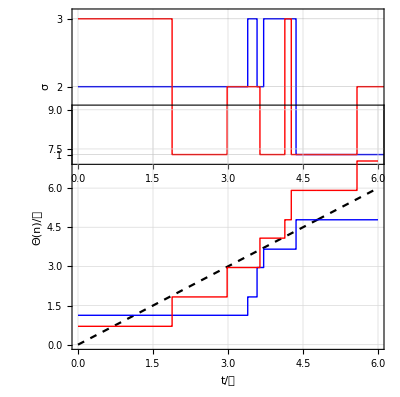

```mathematica
(* Make the plot *)
trajPlot=Plot[{trajFunction[traj1,x],trajFunction[traj2,x]},{x,0,10},PlotRange->{{0,6},{0.9,3.1}}, Frame->True, PlotPoints->10^4,PlotStyle->{ {Blue,Thick},{ Red,Thick}},FrameLabel->{None,"σ"},BaseStyle->{FontFamily->"Times New Roman",40},FrameStyle->Directive[Black,Thick],GridLines->{Automatic,{1,2,3}}, AspectRatio->1/6,FrameTicks->{{{1,2,3},None},{Automatic,None}}];
estPlot=Plot[{x,trajFunction[Θ1,x],trajFunction[Θ2,x]},{x,0,6},PlotRange->{{0,6},{0,9}},PlotPoints->10^4,Frame->True, PlotStyle->{ {Black,Dashed},{Blue,Thick},{ Red,Thick}},FrameLabel->{"t/𝒯","Θ(n)/𝒯"},BaseStyle->{FontFamily->"Times New Roman",40},FrameStyle->Directive[Black,Thick],GridLines->Automatic, AspectRatio->1/3];
trajPlots=GraphicsColumn[{trajPlot,estPlot},Spacings->-45]
```

## Estimators (Fig. 3)

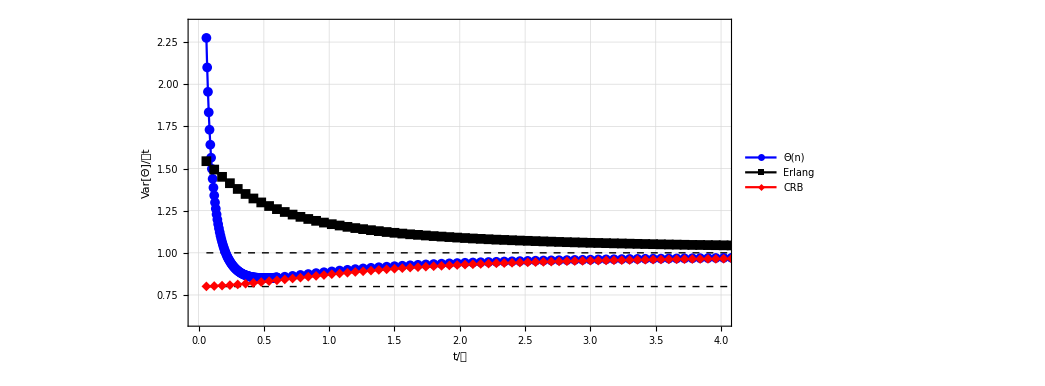

```mathematica
(* For a given n, time t, and escape rates from the first and the second bath, h = Γ1 and g = Γ2, generate a list of probabilities corresponding to: {(n, n) with initial state 1, (n, n) with initial state is 2, (n, n+1), (n+1, n)}. 
For numerical purpose, the optional argument ϵ specifies a precision limit, below which the probability is set to 0.
The probabilities are obtained using the expressions in Appendix D. We require h > g without loss of generality. *)
Prob[h_, g_,n_, t_, ϵ_:0.00001]:=Module[{p1, p2, P1, P2, Pn1n, Pnn1},
p1=(g)/(h+g);
p2 = (h)/(h+g);
Pnn1=p2 h^n g^n 1/Gamma[1+n](-1)^n ⅇ^(-((g+h) t)) t^(2 n) (ⅇ^(h t) HypergeometricU[n,1+2 n,(g-h) t]-ⅇ^(g t) n HypergeometricU[1+n,1+2 n,(-g+h) t]);
Pn1n=p1 h^n g^n 1/Gamma[1+n](-1)^n ⅇ^(-((g+h) t)) t^(2 n) (ⅇ^(g t) HypergeometricU[n,1+2 n,(-g+h) t]-ⅇ^(h t) n HypergeometricU[1+n,1+2 n,(g-h) t]);

P1=p1 h^n g^(n-1)1/(√π t Gamma[n])ⅇ^(-1/2 (g+h) t) (-(g-h)^2)^(-2 n) ((-1)^n (-g+h)^(2 n) ((g-h) t)^(1/2+n) BesselK[-1/2+n,1/2 (g-h) t]+(-1)^n (g-h)^(2 n) ((-g+h) t)^(1/2+n) BesselK[-1/2+n,1/2 (-g+h) t]);
P2=p2 h^(n-1) g^n 1/(√π t Gamma[n])ⅇ^(-1/2 (g+h) t) (-(g-h)^2)^(-2 n) ((-1)^n (-g+h)^(2 n) ((g-h) t)^(1/2+n) BesselK[-1/2+n,1/2 (g-h) t]+(-1)^n (g-h)^(2 n) ((-g+h) t)^(1/2+n) BesselK[-1/2+n,1/2 (-g+h) t]);
{Re[P1]UnitStep[Re[P1]-ϵ] ,Re[P2]UnitStep[ Re[P2]-ϵ] ,Re[ Pnn1]UnitStep[Re[ Pnn1]-ϵ] ,Re[ Pn1n]UnitStep[Re[ Pn1n]-ϵ]}
]
(* Generate the average and the variance of the estimator Θ(σ) in Eq.(12). The argument nmax is a truncation cutoff. *)
Estimator[h_, g_, t_, nmax_,ϵ_:0.00001]:=Module[{n, avg, sq},
avg =0;
sq = 0;
Do[avg = avg+{(n/h+n/g),(n/h+n/g),(n/h+(n+1)/g),((n+1)/h+n/g)}.Prob[h, g, n, t,ϵ]; sq = sq+{(n/h+n/g)^2,(n/h+n/g)^2,(n/h+(n+1)/g)^2,((n+1)/h+n/g)^2}.Prob[h, g, n, t, ϵ], {n, 0, nmax, 1}];
{avg, sq-avg^2}
]
(* Generate the average and the variance of the Erlang estimator. The argument nmax is a truncation cutoff. *)
Erlang[h_, g_, t_, nmax_,ϵ_:0.00001]:=Module[{avg, sq},
avg =0;
sq = 0;
Do[avg = avg+{(((n-1)(h+g))/(h g)),((n(h+g))/(h g)),((n(h+g))/(h g)),((n(h+g))/(h g))}.Prob[h, g, n, t, ϵ]; sq = sq+{(((n-1)(h+g))/(h g))^2,((n(h+g))/(h g))^2,((n(h+g))/(h g))^2,((n(h+g))/(h g))^2}.Prob[h, g, n, t, ϵ], {n, 0, nmax, 1}];
{avg, sq-avg^2}
]
(*Compute the Fisher information for a given time t*)
Fisher[h_, g_,t_,nmax_:20, ϵ_:0.00001]:=Module[{p1, p2, P1, P2, Pn1n, Pnn1, dP1, dP2, dPn1n, dPnn1, tt, fisher},
p1=(g)/(h+g);
p2 = (h)/(h+g);
(*probabilities of trajectories for a given n and time τ: (n, n+1), (n+1, n) , (n, n) with initial state 1, (n, n) with initial state 2*)
Pnn1[n_,τ_]:=(p2 h^n g^n)/Gamma[1+n](-1)^n ⅇ^(-((g+h) τ)) τ^(2 n) (ⅇ^(h τ) HypergeometricU[n,1+2 n,(g-h) τ]-ⅇ^(g τ) n HypergeometricU[1+n,1+2 n,(-g+h) τ]);
Pn1n[n_,τ_]:= (p1 h^n g^n)/Gamma[1+n](-1)^n ⅇ^(-((g+h) τ)) τ^(2 n) (ⅇ^(g τ) HypergeometricU[n,1+2 n,(-g+h) τ]-ⅇ^(h τ) n HypergeometricU[1+n,1+2 n,(g-h) τ]);
P1[n_,τ_]:=(p1 h^n g^(n-1))/(√π τ Gamma[n])ⅇ^(-1/2 (g+h) τ) (-(g-h)^2)^(-2 n) ((-1)^n (-g+h)^(2 n) ((g-h) τ)^(1/2+n) BesselK[-1/2+n,1/2 (g-h) τ]+(-1)^n (g-h)^(2 n) ((-g+h) τ)^(1/2+n) BesselK[-1/2+n,1/2 (-g+h) τ]);
P2[n_, τ_]:=(p2 h^(n-1) g^n)/(√π τ Gamma[n])ⅇ^(-1/2 (g+h) τ) (-(g-h)^2)^(-2 n) ((-1)^n (-g+h)^(2 n) ((g-h) τ)^(1/2+n) BesselK[-1/2+n,1/2 (g-h) τ]+(-1)^n (g-h)^(2 n) ((-g+h) τ)^(1/2+n) BesselK[-1/2+n,1/2 (-g+h) τ]);

(*Time τ derivatives of Log of probabilities of trajectories *)
dPnn1[n_, τ_]:=D[Log[Pnn1[n, tt]], {tt, 1}]/.tt->τ;
dPn1n[n_, τ_]:=D[Log[Pn1n[n, tt]], {tt, 1}]/.tt->τ;
dP1[n_, τ_]:=D[Log[P1[n, tt]], {tt, 1}]/.tt->τ;
dP2[n_, τ_]:=D[Log[P2[n, tt]], {tt, 1}]/.tt->τ;

(* Obtain the Fisher information
For numerical reasons, we impose a cutoff on probabilities at ϵ, setting them to 0*)
fisher = 0;
Do[If[Re[Pnn1[n, t]]>ϵ, fisher=fisher +Re[Pnn1[n, t]]Re[dPnn1[n, t]]^2 , fisher =fisher], {n, 0, nmax, 1}];
Do[If[Re[Pn1n[n, t]]>ϵ, fisher=fisher +Re[Pn1n[n, t]]Re[dPn1n[n, t]]^2 , fisher =fisher], {n, 0, nmax, 1}];
Do[If[Re[P1[n, t]]>ϵ, fisher=fisher +Re[P1[n, t]]Re[dP1[n, t]]^2 , fisher =fisher], {n, 1, nmax, 1}];
Do[If[Re[P2[n, t]]>ϵ, fisher=fisher +Re[P2[n, t]]Re[dP2[n, t]]^2 , fisher =fisher], {n, 1, nmax, 1}];

fisher
]


(* Prepare a list of the quantity to be  plotted with the horizontal axis t/𝒯 *)

h = 0.15; (* Set Γ1*)
g = 0.05; (* Set Γ2*)
(* Compute steady-state probabilities *)
p1=(g)/(h+g);
p2 = (h)/(h+g);
𝒯=p1/h+p2/g; (* Calculate the mean waiting time *)
𝒜= (p1 h +p2 g ); (* Calculate the dynamical activity *)
nmax = 20;
tmax = 100;
tmaxShort=10;
DynAct=Table[{t/𝒯,  1/(𝒯 𝒜)}, {t, 1, tmax}];(* dynamical activity bound *)
WaitTime = Table[{t/𝒯, 1}, {t, 1, tmax}]; (* mean waiting time bound*)
varEstShort= Table[{t/𝒯, (Estimator[h, g, t, nmax][[2]])/(𝒯 t)}, {t, 1, tmaxShort, 0.1}]; (* Variance of the estimator in Eq.(12), part 1 *)
varEstLong= Table[{t/𝒯, (Estimator[h, g, t, nmax][[2]])/(𝒯 t)}, {t, tmaxShort, tmax}];(* Variance of the estimator in Eq.(12), part 2 *)
varEst= Join[varEstShort, varEstLong];
varErl= Table[{t/𝒯, (Erlang[h, g, t, nmax][[2]])/(𝒯 t)}, {t, 1, tmax}];(* Variance of the Erlang estimator  *)
invFisher=Table[{t/𝒯, (1/Fisher[h, g, t, 20])/(𝒯 t)}, {t, 1, tmax}]; (* Cramer Rao bound  *)


(* Prepare the plot *)

estimators=ListLinePlot[{varEst, varErl, invFisher, DynAct,WaitTime},GridLines->Automatic, PlotRange->{{0,4},{0.6,2.35}}, Frame->True,Joined->True, PlotStyle->{ Blue, Black,Red,{Black,Dashed,Thick} ,{Black,Dashed,Thick}},PlotMarkers->{{Automatic,Medium},{Automatic,Medium},{Automatic,Medium},None,None},Frame->True,FrameLabel->{"t/𝒯","Var[Θ]/𝒯t"},BaseStyle->{FontFamily->"Times New Roman",40},FrameStyle->Directive[Black,Thick],GridLines->Automatic,PlotLegends->Placed[{Style["Θ(n)",FontFamily->"Times New Roman",40], Style["Erlang",FontFamily->"Times New Roman",40],Style["CRB" ,FontFamily->"Times New Roman",40]},{0.8,0.65}], AspectRatio->1/2]
```

## Activity measures for random networks (Fig. 4)

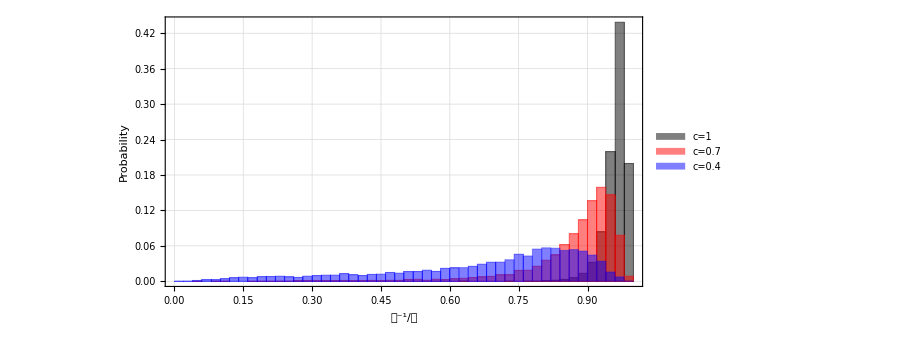

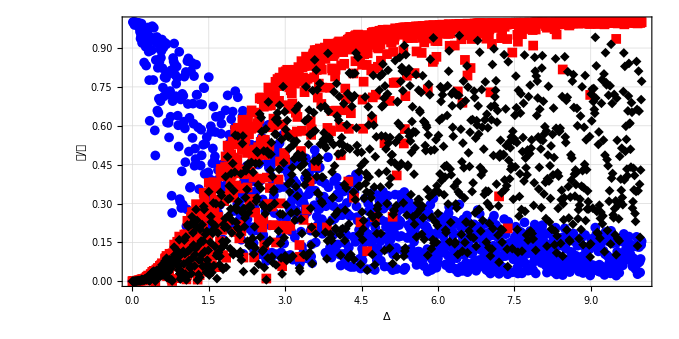

```mathematica
(* Ratio between 𝒯^-1 and 𝒜 for sparse random graphs with connectivity f (called c in the manuscript)*)
activityRatio[f_,d_]:=Module[{L,p,𝒜,𝒯,𝒮},
L=randomSparseGraph[f,d];
p=steadyState[L];
{𝒜,𝒯,𝒮}=activities[L,p];
1/(𝒜 𝒯)
]
(* Make a table of ratios for three different f values and plot the histogram *)
d=10; fs={1,0.7,0.4};
actTab=Table[activityRatio[f,d],{f,fs},{1*^4}];//Quiet
hist=Histogram[actTab,30,Probability,Frame->True,FrameLabel->{"𝒯^-1/𝒜","Probability"},BaseStyle->{FontFamily->"Times New Roman",40},FrameStyle->Directive[Black,Thick],GridLines->Automatic,AspectRatio->1/2,ChartStyle->{Black,Red,Blue},ChartLegends->Placed[Style["c="<>ToString[#],FontFamily->"Times New Roman",30]&/@fs,{0.27,0.54}]]

(* Output the SNR and corresponding TUR, KUR, and CUR bounds for random rings with entropy production quantified by s, allowing for some disorder in s within the range ±ds *) 
snrRingBounds[d_,s_, ds_,w_]:=Module[{gamR,gamL,deltaS,L,p,J,D,A,T,Σ,snr,TURR,KURR,AWTR},
gamR=RandomReal[1,{1,d}];
deltaS=RandomReal[{s-ds/2,s+ds/2},{1,d}];
gamL=gamR*Exp[-deltaS];
L=randomRing[Join[gamR,gamL]];
p=steadyState[L];
J=meanCurrent[L,p,w];
D=diffusionCoeff[L,p,w];
{A,T,Σ}=activities[L,p];
TURR=2 J^2/(D Σ);KURR=J^2/(D A);AWTR=J^2 T/D;
{TURR, KURR, AWTR}
]

(* Cost-precision ratio, fixed entropy production, d=10 *)
sList=Subdivide[10,1000];
d=10;
w=ConstantArray[0,{d,d}];
w[[2,1]]=1;w[[1,2]]=-1;
bounds=Table[snrRingBounds[d,s,0,w],{s,sList}];//Quiet
boundPlot=ListPlot[{Partition[Riffle[sList,bounds[[;;,1]]],2],Partition[Riffle[sList,bounds[[;;,3]]],2],Partition[Riffle[sList,bounds[[;;,2]]],2]},PlotStyle->{Blue,Red,Black},PlotMarkers->{{Automatic,Medium},{Automatic,Medium},{Automatic,Medium}},Frame->True,FrameLabel->{"Δ","𝒮/𝒞"},BaseStyle->{FontFamily->"Times New Roman",40},FrameStyle->Directive[Black,Thick],GridLines->Automatic,AspectRatio->1/2]
```

## KUR violation (Fig. 5)

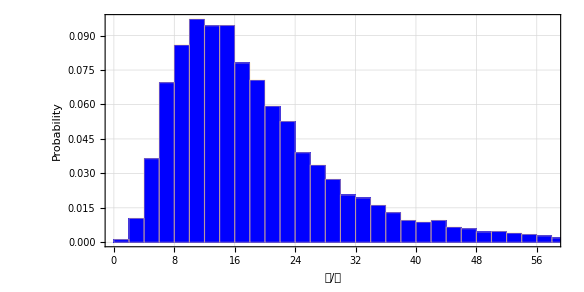

```mathematica
(* Variance of the dimensionless time observable T(σ,t) *)
Tvariance[L_]:=Module[{p,d,u,R},
p=steadyState[L];
d=Length[p];
R=L-DiagonalMatrix[Diagonal[L]];
u=ConstantArray[1,d];
-2u.R.DrazinInverse[L].R.p
]
(* Ratio of the above variance to the dynamical activity, equivalent to the SNR of T(σ,t) in units of 𝒜 *)
Tratio[L_]:=Module[{S,A,T},
{A,T,S}=activities[L,steadyState[L]];
A/Tvariance[L]
]
(* Compute this ratio for random graphs and plot the histogram *)
f=1;d=10;
ratioTab=Table[Tratio[randomSparseGraph[f,d]],{1*^4}];
KURhist=Histogram[ratioTab,Automatic,Probability,Frame->True,FrameLabel->{"𝒮/𝒜","Probability"},BaseStyle->{FontFamily->"Times New Roman",40},FrameStyle->Directive[Black,Thick],GridLines->Automatic,AspectRatio->1/2,ChartStyle->{Blue}]
```

## Erlang estimator autocorrelation function (Fig. 6)

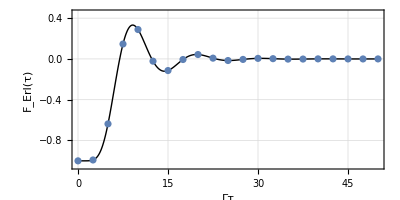

```mathematica
(* Autocorrelation function of the Erlang clock, using an upper cutoff M in the summation for efficiency *)
F[d_,t_,M_]:=d Sum[t^(d-1+m d)Exp[-t]/(d+m d -1)!,{m,0,M}]-1

(* Numerical solution *)
d=10;
gammas={ConstantArray[1,d],ConstantArray[0,d]};
L=randomRing[gammas];
Fnum[t_]:=d MatrixExp[L t][[d,1]]-1
tRange=Subdivide[50,20];
Ftab=Table[{t,Fnum[t]},{t,tRange}];

(* Plot the analytical solution and compare to the exact numerics *)
Fplot=Plot[F[10,t,100],{t,0,50},PlotRange->{{0,50},{-1.05,0.45}},Axes->False,GridLines->Automatic,Frame->True,FrameLabel->{"Γτ","F_Erl(τ)"},PlotStyle->{Black,Thick},BaseStyle->{FontFamily->"Times New Roman",40},FrameStyle->Directive[Black,Thick],AspectRatio->1/2];//Quiet
Show[Fplot,ListPlot[Ftab,PlotRange->Full]]
```

## Allan variance (Fig. 7)

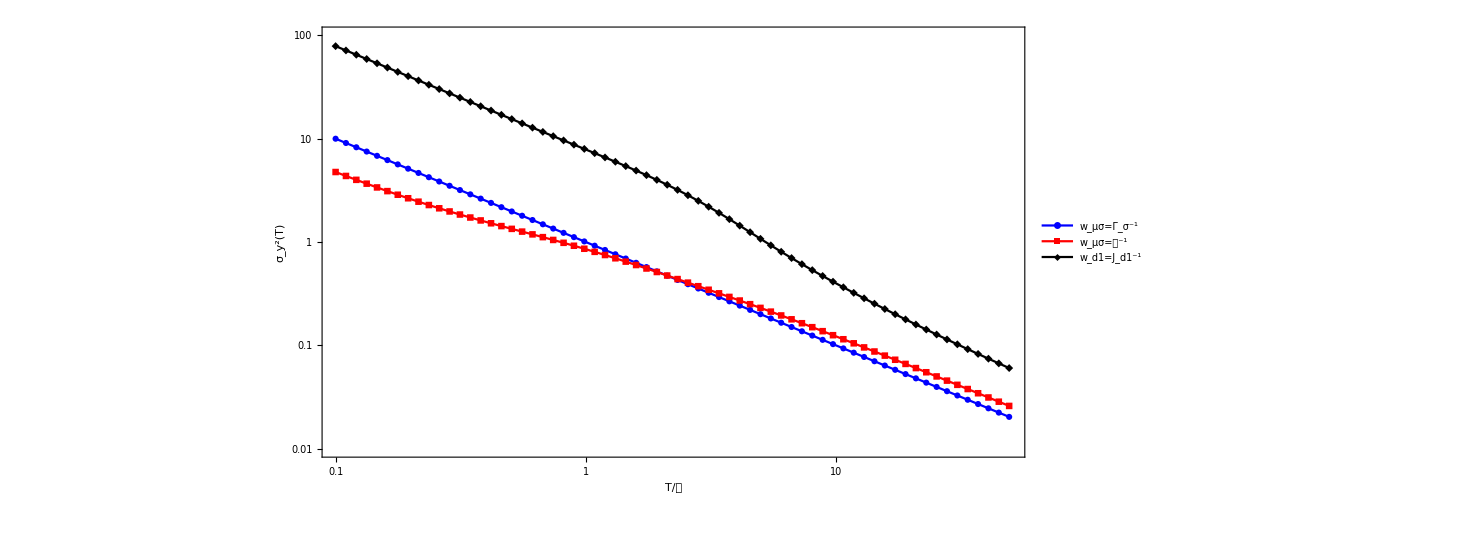

```mathematica
(*Functions to compute the Allan variance *)
aMat[L_,t_]:=Module[{V,Lp,d,Id},
d=Length[L];
Id=IdentityMatrix[d];
V=MatrixExp[L t];
Lp=DrazinInverse[L];
Lp.(V-Id).(2Id-(V-Id)).Lp
]
allanVariance[L_,t_,w_,D_,p_]:=Module[{d,u,W},
d=Length[L];
u=ConstantArray[1,d];
W=w*L;
W=W-DiagonalMatrix[Diagonal[W]];
D/t+u.W.aMat[L,t].W.p/t^2
]

(* Construct a biased ring graph with disordered rates *)
d =10;
s=2; ds=0;
gamR={Sin[Table[2n/3,{n,d}]]^2}//N;
deltaS=RandomReal[{s-ds/2,s+ds/2},{1,d}];
gamL=gamR*Exp[-deltaS];
L=randomRing[Join[gamR,gamL]];
p=steadyState[L];

(* Construct weights for the BLUE, the uniform estimator, and the Erlang estimator, and find their diffusion coefficients *)
Γ=-Diagonal[L];
𝒜=Γ.p;
𝒯=(1/Γ).p;
BLUE=Table[1/Γ,{d}];
Dblue=diffusionCoeff[L,p,BLUE];
Uni=ConstantArray[1/𝒜,{d,d}];
Duni=diffusionCoeff[L,p,Uni];
Erl=ConstantArray[0,{d,d}];
Erl[[1,d]]=(L[[1,d]]p[[d]])^-1;
Derl=diffusionCoeff[L,p,Erl];

(* Compute the Allan variances *)
tList=PowerRange[0.1𝒯,50𝒯,1.1];
aBLUE = Table[{t/𝒯,allanVariance[L,t,BLUE,Dblue,p]},{t,tList}];
aUni =Table[{t/𝒯,allanVariance[L,t,Uni,Duni,p]},{t,tList}];
aErl =Table[{t/𝒯,allanVariance[L,t,Erl,Derl,p]},{t,tList}];

(* Plot the results on log-log scale *)
allan=ListLogLogPlot[{aBLUE,aUni,aErl},PlotRange->{{0.1,50},{0.01,100}},PlotMarkers->Automatic, Joined->True,GridLines->Automatic, PlotRange->{{0,4},{0.6,2.35}}, Frame->True,Joined->True, PlotStyle->{ Blue, Red, Black},PlotMarkers->{{Automatic,Medium},{Automatic,Medium},{Automatic,Medium}},Frame->True,FrameLabel->{"T/𝒯","σ_y^2(T)"},BaseStyle->{FontFamily->"Times New Roman",40},FrameStyle->Directive[Black,Thick],GridLines->Automatic,PlotLegends->Placed[{Style["w_μσ=Γ_σ^-1",FontFamily->"Times New Roman",40], Style["w_μσ=𝒜^-1",FontFamily->"Times New Roman",40], Style["w_d1=J_d1^-1" ,FontFamily->"Times New Roman",40]},{0.85,0.72}], AspectRatio->1/2]
```